```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/Moat-meanfield/MF_DR

```mathematica
fpi1=Import["./sigma0.dat"];
fpi2=Import["./sigma0p2.dat"];
mu=Flatten[Import["./mu.dat"]];
mu2=Table[i,{i,290,310}];
dfpidT1=Table[fpi1[[i]][[1;;-2]]-fpi1[[i]][[2;;-1]],{i,1,60}];
dfpidT2=Table[fpi2[[i]][[1;;-2]]-fpi2[[i]][[2;;-1]],{i,1,15}];
```

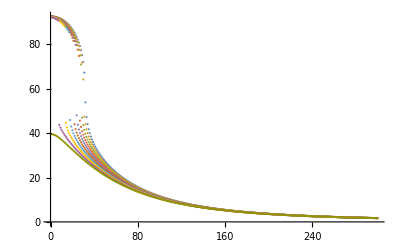

```mathematica
ListPlot[fpi2[[7;;16]],PlotRange->All]
```

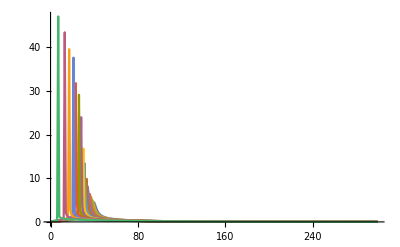

```mathematica
ListLinePlot[dfpidT2[[1;;15]],PlotRange->All]
```

```mathematica
Tpc=Table[Position[dfpidT1[[i]],Max[dfpidT1[[i]]]],{i,1,59}]+0.5//Flatten;
Tpc2={Table[Position[dfpidT2[[i]],Max[dfpidT2[[i]]]],{i,7,15}]+0.5,0.5}//Flatten;
```

```mathematica
pb1=Transpose[{mu[[1;;59]],Tpc}];
pb2=Transpose[{Flatten[{mu2[[7;;15]],305}],Tpc2}]
```

{{296,31.5},{297,30.5},{298,28.5},{299,26.5},{300,23.5},{301,21.5},{302,17.5},{303,13.5},{304,7.5},{305,0.5}}

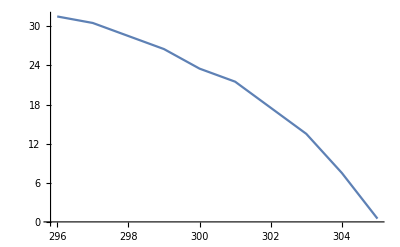

```mathematica
ListLinePlot[pb2]
```

```mathematica
Export["./crossover.dat",pb1]
```

./crossover.dat

```mathematica
Export["./firstorder.dat",pb2]
```

./firstorder.dat